```mathematica
baseNull=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==1&]
```

{0,19683,29524,28764,27246,26487,26488,22708,21951,21954,20439,20448,19692,19696,19686,19684,6561,9490,8784,8757,7374,7293,6642,6670,6588,6562,2187,3160,2917,2430,2460,2214,2190,729,972,1062,810,738,243,364,333,273,244,81,109,84,27,36,9,13,3,1}

```mathematica
repBaseNullGraph=Table[allGraphs[k,"colofournull"]->Labeled[allGraphs[k,"graph"],{k,Style[allGraphs[k,"colofournull"],ColourForKey[allGraphs,k],If[MemberQ[{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key},k],{FontFamily->"Consolas", Italic,Bold,Underlined,20},Plain]]},{Top,Bottom}],{k,baseNull}];
```

```mathematica
repBaseNullGraph2=Table[allGraphs[k,"colofournull"]->allGraphs[k,"colofour"],{k,baseNull}]
```

{p1x2x3x4x5→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p12x3x4x5→v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p12345→v1x2x3x4x5,p1234x5→v15x2x3x4+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1235x4→v14x2x3x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p123x4x5→v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p123x45→v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p1245x3→v13x2x4x5+v1x23x4x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p124x3x5→v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p124x35→v13x25x4+v13x2x45+v13x2x4x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p125x3x4→v134x2x5+v13x24x5+v13x2x45+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p125x34→v13x24x5+v13x2x45+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p12x34x5→v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p12x345→v13x24x5+v13x25x4+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5,p12x35x4→v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p12x3x45→v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p13x2x4x5→v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1345x2→v12x3x4x5+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5,p134x25→v12x35x4+v12x3x45+v12x3x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p134x2x5→v125x3x4+v12x35x4+v12x3x45+v12x3x4x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p135x24→v12x34x5+v12x3x45+v12x3x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p135x2x4→v124x3x5+v12x34x5+v12x3x45+v12x3x4x5+v14x23x5+v14x25x3+v14x2x3x5+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p13x24x5→v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p13x245→v12x34x5+v12x35x4+v12x3x4x5+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p13x25x4→v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p13x2x45→v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p14x2x3x5→v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p145x23→v12x34x5+v12x35x4+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p145x2x3→v123x4x5+v12x34x5+v12x35x4+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p14x23x5→v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p14x235→v12x34x5+v12x3x45+v12x3x4x5+v13x24x5+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p14x25x3→v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p14x2x35→v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p15x2x3x4→v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p15x23x4→v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p15x234→v12x35x4+v12x3x45+v12x3x4x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p15x24x3→v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p15x2x34→v123x45+v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x23x4x5→v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x2345→v12x3x4x5+v13x2x4x5+v14x2x3x5+v15x2x3x4+v1x2x3x4x5,p1x234x5→v125x3x4+v12x35x4+v12x3x45+v12x3x4x5+v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x2x3x4+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x235x4→v124x3x5+v12x34x5+v12x3x45+v12x3x4x5+v134x2x5+v13x24x5+v13x2x45+v13x2x4x5+v145x2x3+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p1x23x45→v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p1x24x3x5→v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x245x3→v123x4x5+v12x34x5+v12x35x4+v12x3x4x5+v134x2x5+v135x2x4+v13x2x4x5+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x4x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,p1x24x35→v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p1x25x3x4→v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x25x34→v123x45+v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x2x34x5→v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x3x4+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,p1x2x345→v123x4x5+v124x3x5+v125x3x4+v12x3x4x5+v13x24x5+v13x25x4+v13x2x4x5+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5,p1x2x35x4→v1234x5+v123x45+v123x4x5+v1245x3+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,p1x2x3x45→v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5}

```mathematica
allGraphs[alfa1Key,"colofournull"]/.repBaseNullGraph
```

1/12 (-2 -Graphics-p12x3x4x5+4 -Graphics-p13x2x4x5-2 -Graphics-p14x2x3x5-2 -Graphics-p1x23x4x5+4 -Graphics-p1x24x3x5-2 -Graphics-p1x2x34x5+2 -Graphics-p12x35x4+2 -Graphics-p12x3x45-4 -Graphics-p13x25x4-4 -Graphics-p13x2x45+2 -Graphics-p14x25x3+2 -Graphics-p14x2x35+2 -Graphics-p15x23x4-4 -Graphics-p15x24x3+2 -Graphics-p15x2x34+2 -Graphics-p1x23x45-4 -Graphics-p1x24x35+2 -Graphics-p1x25x34+2 -Graphics-p125x3x4-4 -Graphics-p135x2x4+2 -Graphics-p145x2x3+2 -Graphics-p1x235x4-4 -Graphics-p1x245x3+2 -Graphics-p1x2x345--Graphics-p123x45--Graphics-p124x35--Graphics-p125x34--Graphics-p12x345--Graphics-p134x25+5 -Graphics-p135x24+5 -Graphics-p13x245--Graphics-p145x23--Graphics-p14x235--Graphics-p15x234+-Graphics-p1234x5--Graphics-p1235x4--Graphics-p1245x3--Graphics-p1345x2--Graphics-p1x2345+-Graphics-p12345)

```mathematica
ineqsnull=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofournull"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
Take[ineqsnull,4]
```

{p1x2x3x4x5>0,p12x3x4x5>0,1/2 (p123x4x5+p12x3x4x5+p13x2x4x5-p1x23x4x5)>0,1/6 (p1234x5+2 p123x4x5+2 p124x3x5-p12x34x5+2 p12x3x4x5+2 p134x2x5-p13x24x5+2 p13x2x4x5-p14x23x5+2 p14x2x3x5-p1x234x5-p1x23x4x5-p1x24x3x5-p1x2x34x5)>0}

```mathematica
ineqsnullsimp=AndToTable[Fold[And,ineqsnull]//Simplify];Take[ineqsnullsimp,3]
```

{p1x2x3x4x5>0,p12x3x4x5>0,p123x4x5>0}

```mathematica
Length[ineqsnullsimp]
```

1805

```mathematica
Select[ineqsnullsimp,Length[#[[1]]]+Length[#[[2]]]<3&]
```

{p1x2x3x4x5>0,p12x3x4x5>0,p123x4x5>0,p13x2x4x5>0,p1x23x4x5>0,p1234x5≥0,p12x34x5>0,p13x24x5>0,p14x23x5>0,p124x3x5>0,p134x2x5>0,p14x2x3x5>0,p1x234x5>0,p1x24x3x5>0,p1x2x34x5>0,p12345==0,p1235x4≥0,p123x45>0,p1245x3≥0,p124x35>0,p125x34>0,p125x3x4>0,p12x345>0,p12x35x4>0,p12x3x45>0,p1345x2≥0,p134x25>0,p135x24>0,p135x2x4>0,p13x245>0,p13x25x4>0,p13x2x45>0,p145x23>0,p145x2x3>0,p14x235>0,p14x25x3>0,p14x2x35>0,p15x234>0,p15x23x4>0,p15x24x3>0,p15x2x34>0,p15x2x3x4>0,p1x2345≥0,p1x235x4>0,p1x23x45>0,p1x245x3>0,p1x24x35>0,p1x25x34>0,p1x25x3x4>0,p1x2x345>0,p1x2x35x4>0,p1x2x3x45>0,p123x45<p123x4x5,p124x35<p124x3x5,p125x34<p125x3x4,p12x34x5<p12x3x4x5,p12x35x4<p12x3x4x5,p12x3x45<p12x3x4x5,p12x3x4x5<p1x2x3x4x5,p12x34x5<p1x2x34x5,p12x345<p1x2x345,p12x35x4<p1x2x35x4,p12x3x45<p1x2x3x45,p134x25<p134x2x5,p135x24<p135x2x4,p13x24x5<p13x2x4x5,p13x25x4<p13x2x4x5,p13x2x45<p13x2x4x5,p13x2x4x5<p1x2x3x4x5,p13x24x5<p1x24x3x5,p13x245<p1x245x3,p13x25x4<p1x25x3x4,p13x2x45<p1x2x3x45,p145x23<p145x2x3,p14x23x5<p14x2x3x5,p14x25x3<p14x2x3x5,p14x2x35<p14x2x3x5,p14x2x3x5<p1x2x3x4x5,p14x23x5<p1x23x4x5,p14x235<p1x235x4,p14x25x3<p1x25x3x4,p14x2x35<p1x2x35x4,p15x23x4<p15x2x3x4,p15x24x3<p15x2x3x4,p15x2x34<p15x2x3x4,p15x2x3x4<p1x2x3x4x5,p15x23x4<p1x23x4x5,p15x234<p1x234x5,p15x24x3<p1x24x3x5,p15x2x34<p1x2x34x5,p1x23x45<p1x23x4x5,p1x23x4x5<p1x2x3x4x5,p1x23x45<p1x2x3x45,p1x24x35<p1x24x3x5,p1x24x3x5<p1x2x3x4x5,p1x24x35<p1x2x35x4,p1x25x34<p1x25x3x4,p1x25x3x4<p1x2x3x4x5,p1x25x34<p1x2x34x5,p1x2x34x5<p1x2x3x4x5,p1x2x35x4<p1x2x3x4x5,p1x2x3x45<p1x2x3x4x5}

```mathematica
Map[Simplify[#]&,Take[Select[ineqsnullsimp,2<=Length[#[[1]]]+Length[#[[2]]]≤4&]/.repBaseNullGraph2,1]]/.repcolofour5base
```

{-Graphics-v15x234+-Graphics-v1x2345+-Graphics-v14x235+-Graphics-v145x23+-Graphics-v14x23x5+-Graphics-v15x23x4+-Graphics-v1x234x5+-Graphics-v1x235x4+-Graphics-v1x23x45+-Graphics-v1x23x4x5>0}

```mathematica
repValue=Table[allGraphs[k,"colofour"]->If[ToString[allGraphs[k,"comp"]]=="Greater",1,0],{k,baseKeys5}]
```

{v12345→1,v1234x5→1,v1235x4→1,v123x45→1,v123x4x5→1,v1245x3→1,v124x35→0,v124x3x5→0,v125x34→1,v125x3x4→1,v12x345→1,v12x34x5→1,v12x35x4→0,v12x3x45→1,v12x3x4x5→0,v1345x2→1,v134x25→0,v134x2x5→0,v135x24→0,v135x2x4→0,v13x245→0,v13x24x5→0,v13x25x4→0,v13x2x45→0,v13x2x4x5→0,v145x23→1,v145x2x3→1,v14x235→0,v14x23x5→0,v14x25x3→0,v14x2x35→0,v14x2x3x5→0,v15x234→1,v15x23x4→1,v15x24x3→0,v15x2x34→1,v15x2x3x4→0,v1x2345→1,v1x234x5→1,v1x235x4→0,v1x23x45→1,v1x23x4x5→0,v1x245x3→0,v1x24x35→0,v1x24x3x5→0,v1x25x34→0,v1x25x3x4→0,v1x2x345→1,v1x2x34x5→0,v1x2x35x4→0,v1x2x3x45→0,v1x2x3x4x5→0}

```mathematica
ExpressionToTable[DeleteDuplicates[Map[Simplify[#]/.repBaseNullGraph2&,Select[ineqsnullsimp,(#[[1]]/.repBaseNullGraph2/.repValue)+(#[[2]]/.repBaseNullGraph2/.repValue)==0&]]]]
```

v1x2x3x4x5==0
v15x2x3x4+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5≥0
v12x3x4x5+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5≥0
v12x3x4x5+v13x2x4x5+v14x2x3x5+v15x2x3x4+v1x2x3x4x5≥0
v14x2x3x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5≥0
v13x2x4x5+v1x23x4x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5≥0

```mathematica
ExpressionToTable[DeleteDuplicates[Map[{#[[1]],#[[2]]}&,Select[ineqsnullsimp,(#[[1]]/.repBaseNullGraph2/.repValue)+(#[[2]]/.repBaseNullGraph2/.repValue)==1&]]]]/.repBaseNullGraph2/.demoValues
```

104 | 0
122 | 0
114 | 0
114 | 0
122 | 0

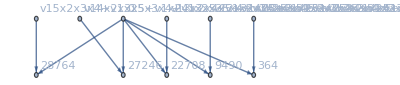

```mathematica
Graph[{v15x2x3x4+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5->28764,0->28764,v14x2x3x5+v1x24x3x5+v1x2x34x5+v1x2x3x45+v1x2x3x4x5->27246,0->27246,v13x2x4x5+v1x23x4x5+v1x2x34x5+v1x2x35x4+v1x2x3x4x5->22708,0->22708,v12x3x4x5+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5->9490,0->9490,v12x3x4x5+v13x2x4x5+v14x2x3x5+v15x2x3x4+v1x2x3x4x5->364,0->364},VertexLabels->"Name"]
```